```mathematica
Clear[lambda]
lambda =0.4;
```

```mathematica
Clear[fequilibria,f1,f2,f3]
fequilibria=NSolve[lambda*f==-1/(1+Abs[f])+(2/6)/((1/6)+Abs[f]),f];
If[lambda <0.333801,{f1,f2,f3}={fequilibria[[1]],fequilibria[[2]],fequilibria[[3]]},f3=fequilibria[[1]]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{f→0.198069}

```mathematica
Clear[x1,y1, x2,y2, x3,y3]
If[lambda<0.333801,{{x1,y1},{x2,y2},{x3,y3}}=
{{(1/6)/((1/6)+Abs[f]),1/(1+Abs[f])}/.f1,
{(1/6)/((1/6)+Abs[f]),1/(1+Abs[f])}/. f2,
{(1/6)/((1/6)+Abs[f]),1/(1+Abs[f])}/. f3},
{x3,y3}={(1/6)/((1/6)+Abs[f]),1/(1+Abs[f])}/. f3]
```

{0.456952,0.834677}

```mathematica
g[x_,y_,delta_]:=delta*(1-x)-Abs[(1/lambda)*(-y+2*x)]*x 
h[x_,y_]:=1-y-Abs[(1/lambda)*(-y+2*x)]*y
```

```mathematica
gneg[x_,y_,delta_]:=delta*(1-x)-(-(1/lambda)*(-y+2*x))*x
hneg[x_,y_] :=1-y-(-(1/lambda)*(-y+2*x))*y
```

```mathematica
gplus[x_,y_,delta_]:=delta*(1-x)-((1/lambda)*(-y+2*x))*x
hplus[x_,y_]:=1-y-((1/lambda)*(-y+2*x))*y
```

```mathematica
MatrixForm[Jneg={{D[gneg[x,y,1/6],x],D[gneg[x,y,1/6],y]},{D[hneg[x,y], x],D[hneg[x,y],y]}}]
```

(-1/6+5. x+2.5 (2 x-y) | -2.5 x
5. y | -1+2.5 (2 x-y)-2.5 y)

```mathematica
If[lambda <0.333801,MatrixForm[J1=Jneg/.{x-> x1,y->y1}],Print["There are no equilibria with f <0"]]
```

There are no equilibria with f <0

```mathematica
If[lambda<0.333801,Eigenvalues[J1],Print["Only one equilibrium (×3,y3)"]]
If[lambda<0.333801,Eigenvectors[J1],Print["Only one equilibrium (×3,y3)"]]
```

Only one equilibrium (×3,y3)

Only one equilibrium (×3,y3)

```mathematica
If[lambda<0.333801,MatrixForm[J2=Jneg/. {x -> x2,y->y2}],Print["There are no equilibria with f <0"]]
```

There are no equilibria with f <0

```mathematica
If[lambda<0.333801,Eigenvalues[J2],Print["Only one equilibrium (×3,y3)"]]
If[lambda<0.333801,Eigenvectors[J2],Print["Only one equilibrium (x3,y1)"]]
```

Only one equilibrium (×3,y3)

Only one equilibrium (x3,y1)

```mathematica
MatrixForm[Jplus={{D[gplus[x,y,1/6],x],D[gplus[x,y,1/6],y]},{D[hplus[x,y],x],D[hplus[x,y],y]}}]
```

(-1/6-5. x-2.5 (2 x-y) | 2.5 x
-5. y | -1-2.5 (2 x-y)+2.5 y)

```mathematica
MatrixForm[J3=Jplus/. {x -> x3,y->y3}]
```

(-2.6495 | 1.14238
-4.17338 | 0.888622)

```mathematica
Eigenvalues[J3]
Eigenvectors[J3]
```

{-0.880437+1.27985 ⅈ,-0.880437-1.27985 ⅈ}

{{0.375591-0.271727 ⅈ,0.886056+0. ⅈ},{0.375591+0.271727 ⅈ,0.886056+0. ⅈ}}

```mathematica
If[lambda<0.333801,
Show[
ContourPlot[(1/lambda)*(-y+2*x)==0,
{x,0,1},{y,0,1},
ContourStyle->Directive[Darker[Green],Thick],
FrameLabel->{"x (salinity)","y (temperature)"}],
Graphics[{Red,Disk[{x,y}/. {x ->x1,y->y1},0.01],
Disk[{x,y}/. {x -> x2,y->y2},0.01],
Disk[{x,y}/.{x ->x3,y->y3},0.01]}],
Show[ContourPlot[(1/lambda)*(-y+2*x)==0,{x,0,1},{y,0,1},ContourStyle->Directive[Darker[Green],Thick],FrameLabel->{"× (salinity)","y (temperature)"},LabelStyle->Bold],StreamPlot[{g[x,y,1/6],h[x,y]},{x,0,1},{y,0,1}]],
Graphics[{Red,Disk[{x,y}/. {x->x3,y->y3},0.01]}],
StreamPlot[{g[x,y,1/6],h[x,y]},{x,0,1},{y,0,1}]]]
```

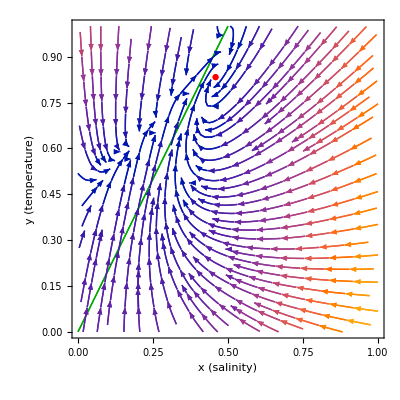

```mathematica
If[lambda>0.333801,
Show[
ContourPlot[(1/lambda)*(-y+2*x)==0,
{x,0,1},{y,0,1},
ContourStyle->Directive[Darker[Green],Thick],
FrameLabel->{"x (salinity)","y (temperature)"}],
Graphics[{Red,Disk[{x,y}/. {x ->x3,y->y3},0.01]}],
Show[ContourPlot[(1/lambda)*(-y+2*x)==0,{x,0,1},{y,0,1},
ContourStyle->Directive[Darker[Green],Thick],
FrameLabel->{"× (salinity)","y (temperature)"}],
StreamPlot[{g[x,y,1/6],h[x,y]},{x,0,1},{y,0,1}]],
Graphics[{Red,Disk[{x,y}/. {x->x3,y->y3},0.01]}],
StreamPlot[{g[x,y,1/6],h[x,y]},{x,0,1},{y,0,1}]]]
```

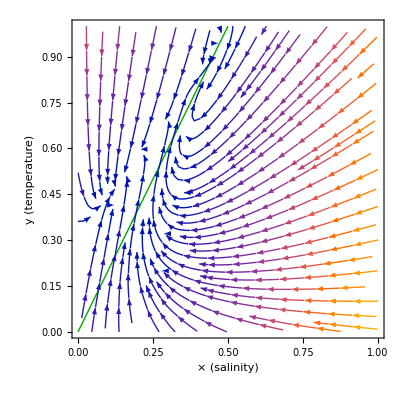

```mathematica
Show[ContourPlot[(1/lambda)*(-y+2*x)==0,{x,0,1},{y,0,1},ContourStyle->Directive[Darker[Green],Thick],FrameLabel->{"× (salinity)","y (temperature)"},LabelStyle->Bold],StreamPlot[{g[x,y,1/6],h[x,y]},{x,0,1},{y,0,1}]]
```